```mathematica
q=0.99; α=0.3;
```

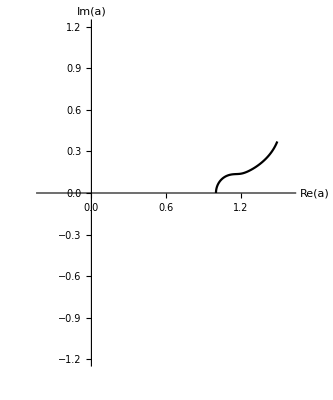

```mathematica
f1=ParametricPlot[ReIm[1+Exp[I*theta] QPochhammer[Exp[-I*theta],q]/QPochhammer[q^α Exp[-I*theta],q]],{theta,2Pi,2Pi+0.2},PlotStyle->Black,AxesLabel->{"Re(a)","Im(a)"},PlotRange->{{-0.4,1.6},{-1.2,1.2}}]
```

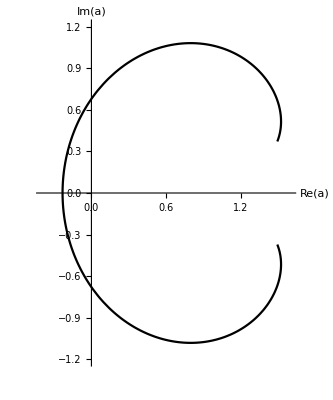

```mathematica
f2=ParametricPlot[ReIm[1+Exp[I*theta] QPochhammer[Exp[-I*theta],q]/QPochhammer[q^α Exp[-I*theta],q]],{theta,2Pi+0.2,4Pi-0.2},PlotStyle->Black,AxesLabel->{"Re(a)","Im(a)"},PlotRange->{{-0.4,1.6},{-1.2,1.2}}]
```

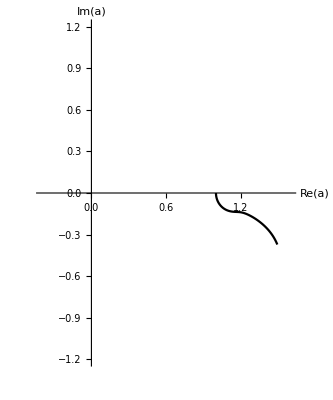

```mathematica
f3=ParametricPlot[ReIm[1+Exp[I*theta] QPochhammer[Exp[-I*theta],q]/QPochhammer[q^α Exp[-I*theta],q]],{theta,4Pi-0.2,4Pi},PlotStyle->Black,AxesLabel->{"Re(a)","Im(a)"},PlotRange->{{-0.4,1.6},{-1.2,1.2}}]
```

```mathematica
(0.4+1.6)/0.05
```

40.

```mathematica
b=Import["C:\\Users\\Sachin\\AppData\\Local\\Programs\\Microsoft VS Code\\blue.csv"];
g=Import["C:\\Users\\Sachin\\AppData\\Local\\Programs\\Microsoft VS Code\\green.csv"];
o=Import["C:\\Users\\Sachin\\AppData\\Local\\Programs\\Microsoft VS Code\\orange.csv"];
```

```mathematica
f4=ListPlot[{b,g,o},PlotStyle->{Blue,Green,Orange},PlotRange->{{-0.4,1.6},{-1.2,1.2}}]
```

ListPlot::lpn: {{{-0.2,-0.25},{-0.2,-0.2},{-0.2,-0.15},{-0.2,-0.1},{-0.2,-0.05},{-0.2,0.},{-0.2,0.05},{-0.2,0.1},{-0.2,0.15},{-0.2,0.2},«1162»},{},{{-0.5,-1.2},{-0.5,-1.15},{-0.5,-1.1},{-0.5,-1.05},{-0.5,-1.},{-0.5,-0.95},{-0.5,-0.9},{-0.5,-0.85},{-0.5,-0.8},{-0.5,-0.75},«1023»}} is not a list of numbers or pairs of numbers.

ListPlot[{1},PlotStyle→{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0]},PlotRange→{{-0.4,1.6},{-1.2,1.2}}]
 |  |  |  |

```mathematica
b
```

{{-0.2,-0.25},{-0.2,-0.2},{-0.2,-0.15},{-0.2,-0.1},{-0.2,-0.05},{-0.2,0.},{-0.2,0.05},{-0.2,0.1},{-0.2,0.15},{-0.2,0.2},{-0.2,0.25},{-0.15,-0.4},{-0.15,-0.35},{-0.15,-0.3},{-0.15,-0.25},{-0.15,-0.2},{-0.15,-0.15},{-0.15,-0.1},{-0.15,-0.05},{-0.15,0.},{-0.15,0.05},{-0.15,0.1},{-0.15,0.15},{-0.15,0.2},{-0.15,0.25},{-0.15,0.3},{-0.15,0.35},{-0.15,0.4},{-0.1,-0.5},{-0.1,-0.45},{-0.1,-0.4},{-0.1,-0.35},{-0.1,-0.3},{-0.1,-0.25},{-0.1,-0.2},{-0.1,-0.15},{-0.1,-0.1},{-0.1,-0.05},{-0.1,0.},{-0.1,0.05},{-0.1,0.1},{-0.1,0.15},{-0.1,0.2},{-0.1,0.25},{-0.1,0.3},{-0.1,0.35},{-0.1,0.4},{-0.1,0.45},{-0.1,0.5},{-0.05,-0.6},{-0.05,-0.55},{-0.05,-0.5},{-0.05,-0.45},{-0.05,-0.4},{-0.05,-0.35},{-0.05,-0.3},{-0.05,-0.25},{-0.05,-0.2},{-0.05,-0.15},{-0.05,-0.1},{-0.05,-0.05},{-0.05,0.},{-0.05,0.05},{-0.05,0.1},{-0.05,0.15},{-0.05,0.2},{-0.05,0.25},{-0.05,0.3},{-0.05,0.35},{-0.05,0.4},{-0.05,0.45},{-0.05,0.5},{-0.05,0.55},{-0.05,0.6},{0.,-0.65},{0.,-0.6},{0.,-0.55},{0.,-0.5},{0.,-0.45},{0.,-0.4},{0.,-0.35},{0.,-0.3},{0.,-0.25},{0.,-0.2},{0.,-0.15},{0.,-0.1},{0.,-0.05},{0.,0.},{0.,0.05},{0.,0.1},{0.,0.15},{0.,0.2},{0.,0.25},{0.,0.3},{0.,0.35},{0.,0.4},{0.,0.45},{0.,0.5},{0.,0.55},{0.,0.6},{0.,0.65},{0.05,-0.7},{0.05,-0.65},{0.05,-0.6},{0.05,-0.55},{0.05,-0.5},{0.05,-0.45},{0.05,-0.4},{0.05,-0.35},{0.05,-0.3},{0.05,-0.25},{0.05,-0.2},{0.05,-0.15},{0.05,-0.1},{0.05,-0.05},{0.05,0.},{0.05,0.05},{0.05,0.1},{0.05,0.15},{0.05,0.2},{0.05,0.25},{0.05,0.3},{0.05,0.35},{0.05,0.4},{0.05,0.45},{0.05,0.5},{0.05,0.55},{0.05,0.6},{0.05,0.65},{0.05,0.7},{0.1,-0.75},{0.1,-0.7},{0.1,-0.65},{0.1,-0.6},{0.1,-0.55},{0.1,-0.5},{0.1,-0.45},{0.1,-0.4},{0.1,-0.35},{0.1,-0.3},{0.1,-0.25},{0.1,-0.2},{0.1,-0.15},{0.1,-0.1},{0.1,-0.05},{0.1,0.},{0.1,0.05},{0.1,0.1},{0.1,0.15},{0.1,0.2},{0.1,0.25},{0.1,0.3},{0.1,0.35},{0.1,0.4},{0.1,0.45},{0.1,0.5},{0.1,0.55},{0.1,0.6},{0.1,0.65},{0.1,0.7},{0.1,0.75},{0.15,-0.8},{0.15,-0.75},{0.15,-0.7},{0.15,-0.65},{0.15,-0.6},{0.15,-0.55},{0.15,-0.5},{0.15,-0.45},{0.15,-0.4},{0.15,-0.35},{0.15,-0.3},{0.15,-0.25},{0.15,0.25},{0.15,0.3},{0.15,0.35},{0.15,0.4},{0.15,0.45},{0.15,0.5},{0.15,0.55},{0.15,0.6},{0.15,0.65},{0.15,0.7},{0.15,0.75},{0.15,0.8},{0.2,-0.85},{0.2,-0.8},{0.2,-0.75},{0.2,-0.7},{0.2,-0.65},{0.2,-0.6},{0.2,-0.55},{0.2,-0.5},{0.2,-0.45},{0.2,-0.4},{0.2,-0.35},{0.2,0.35},{0.2,0.4},{0.2,0.45},{0.2,0.5},{0.2,0.55},{0.2,0.6},{0.2,0.65},{0.2,0.7},{0.2,0.75},{0.2,0.8},{0.2,0.85},{0.25,-0.9},{0.25,-0.85},{0.25,-0.8},{0.25,-0.75},{0.25,-0.7},{0.25,-0.65},{0.25,-0.6},{0.25,-0.55},{0.25,-0.5},{0.25,-0.45},{0.25,-0.4},{0.25,0.4},{0.25,0.45},{0.25,0.5},{0.25,0.55},{0.25,0.6},{0.25,0.65},{0.25,0.7},{0.25,0.75},{0.25,0.8},{0.25,0.85},{0.25,0.9},{0.3,-0.9},{0.3,-0.85},{0.3,-0.8},{0.3,-0.75},{0.3,-0.7},{0.3,-0.65},{0.3,-0.6},{0.3,-0.55},{0.3,-0.5},{0.3,-0.45},{0.3,0.45},{0.3,0.5},{0.3,0.55},{0.3,0.6},{0.3,0.65},{0.3,0.7},{0.3,0.75},{0.3,0.8},{0.3,0.85},{0.3,0.9},{0.35,-0.95},{0.35,-0.9},{0.35,-0.85},{0.35,-0.8},{0.35,-0.75},{0.35,-0.7},{0.35,-0.65},{0.35,-0.6},{0.35,-0.55},{0.35,-0.5},{0.35,0.5},{0.35,0.55},{0.35,0.6},{0.35,0.65},{0.35,0.7},{0.35,0.75},{0.35,0.8},{0.35,0.85},{0.35,0.9},{0.35,0.95},{0.4,-0.95},{0.4,-0.9},{0.4,-0.85},{0.4,-0.8},{0.4,-0.75},{0.4,-0.7},{0.4,-0.65},{0.4,-0.6},{0.4,-0.55},{0.4,0.55},{0.4,0.6},{0.4,0.65},{0.4,0.7},{0.4,0.75},{0.4,0.8},{0.4,0.85},{0.4,0.9},{0.4,0.95},{0.45,-1.},{0.45,-0.95},{0.45,-0.9},{0.45,-0.85},{0.45,-0.8},{0.45,-0.75},{0.45,-0.7},{0.45,-0.65},{0.45,-0.6},{0.45,0.6},{0.45,0.65},{0.45,0.7},{0.45,0.75},{0.45,0.8},{0.45,0.85},{0.45,0.9},{0.45,0.95},{0.45,1.},{0.5,-1.},{0.5,-0.95},{0.5,-0.9},{0.5,-0.85},{0.5,-0.8},{0.5,-0.75},{0.5,-0.7},{0.5,-0.65},{0.5,-0.6},{0.5,0.6},{0.5,0.65},{0.5,0.7},{0.5,0.75},{0.5,0.8},{0.5,0.85},{0.5,0.9},{0.5,0.95},{0.5,1.},{0.55,-1.},{0.55,-0.95},{0.55,-0.9},{0.55,-0.85},{0.55,-0.8},{0.55,-0.75},{0.55,-0.7},{0.55,-0.65},{0.55,-0.6},{0.55,0.6},{0.55,0.65},{0.55,0.7},{0.55,0.75},{0.55,0.8},{0.55,0.85},{0.55,0.9},{0.55,0.95},{0.55,1.},{0.6,-1.05},{0.6,-1.},{0.6,-0.95},{0.6,-0.9},{0.6,-0.85},{0.6,-0.8},{0.6,-0.75},{0.6,-0.7},{0.6,-0.65},{0.6,0.65},{0.6,0.7},{0.6,0.75},{0.6,0.8},{0.6,0.85},{0.6,0.9},{0.6,0.95},{0.6,1.},{0.6,1.05},{0.65,-1.05},{0.65,-1.},{0.65,-0.95},{0.65,-0.9},{0.65,-0.85},{0.65,-0.8},{0.65,-0.75},{0.65,-0.7},{0.65,-0.65},{0.65,0.65},{0.65,0.7},{0.65,0.75},{0.65,0.8},{0.65,0.85},{0.65,0.9},{0.65,0.95},{0.65,1.},{0.65,1.05},{0.7,-1.05},{0.7,-1.},{0.7,-0.95},{0.7,-0.9},{0.7,-0.85},{0.7,-0.8},{0.7,-0.75},{0.7,-0.7},{0.7,-0.65},{0.7,0.65},{0.7,0.7},{0.7,0.75},{0.7,0.8},{0.7,0.85},{0.7,0.9},{0.7,0.95},{0.7,1.},{0.7,1.05},{0.75,-1.05},{0.75,-1.},{0.75,-0.95},{0.75,-0.9},{0.75,-0.85},{0.75,-0.8},{0.75,-0.75},{0.75,-0.7},{0.75,-0.65},{0.75,0.65},{0.75,0.7},{0.75,0.75},{0.75,0.8},{0.75,0.85},{0.75,0.9},{0.75,0.95},{0.75,1.},{0.75,1.05},{0.8,-1.05},{0.8,-1.},{0.8,-0.95},{0.8,-0.9},{0.8,-0.85},{0.8,-0.8},{0.8,-0.75},{0.8,-0.7},{0.8,-0.65},{0.8,-0.6},{0.8,0.6},{0.8,0.65},{0.8,0.7},{0.8,0.75},{0.8,0.8},{0.8,0.85},{0.8,0.9},{0.8,0.95},{0.8,1.},{0.8,1.05},{0.85,-1.05},{0.85,-1.},{0.85,-0.95},{0.85,-0.9},{0.85,-0.85},{0.85,-0.8},{0.85,-0.75},{0.85,-0.7},{0.85,-0.65},{0.85,-0.6},{0.85,0.6},{0.85,0.65},{0.85,0.7},{0.85,0.75},{0.85,0.8},{0.85,0.85},{0.85,0.9},{0.85,0.95},{0.85,1.},{0.85,1.05},{0.9,-1.05},{0.9,-1.},{0.9,-0.95},{0.9,-0.9},{0.9,-0.85},{0.9,-0.8},{0.9,-0.75},{0.9,-0.7},{0.9,-0.65},{0.9,-0.6},{0.9,0.6},{0.9,0.65},{0.9,0.7},{0.9,0.75},{0.9,0.8},{0.9,0.85},{0.9,0.9},{0.9,0.95},{0.9,1.},{0.9,1.05},{0.95,-1.05},{0.95,-1.},{0.95,-0.95},{0.95,-0.9},{0.95,-0.85},{0.95,-0.8},{0.95,-0.75},{0.95,-0.7},{0.95,-0.65},{0.95,-0.6},{0.95,-0.55},{0.95,0.55},{0.95,0.6},{0.95,0.65},{0.95,0.7},{0.95,0.75},{0.95,0.8},{0.95,0.85},{0.95,0.9},{0.95,0.95},{0.95,1.},{0.95,1.05},{1.,-1.05},{1.,-1.},{1.,-0.95},{1.,-0.9},{1.,-0.85},{1.,-0.8},{1.,-0.75},{1.,-0.7},{1.,-0.65},{1.,-0.6},{1.,-0.55},{1.,-0.5},{1.,0.5},{1.,0.55},{1.,0.6},{1.,0.65},{1.,0.7},{1.,0.75},{1.,0.8},{1.,0.85},{1.,0.9},{1.,0.95},{1.,1.},{1.,1.05},{1.05,-1.},{1.05,-0.95},{1.05,-0.9},{1.05,-0.85},{1.05,-0.8},{1.05,-0.75},{1.05,-0.7},{1.05,-0.65},{1.05,-0.6},{1.05,-0.55},{1.05,-0.5},{1.05,-0.45},{1.05,0.45},{1.05,0.5},{1.05,0.55},{1.05,0.6},{1.05,0.65},{1.05,0.7},{1.05,0.75},{1.05,0.8},{1.05,0.85},{1.05,0.9},{1.05,0.95},{1.05,1.},{1.1,-1.},{1.1,-0.95},{1.1,-0.9},{1.1,-0.85},{1.1,-0.8},{1.1,-0.75},{1.1,-0.7},{1.1,-0.65},{1.1,-0.6},{1.1,-0.55},{1.1,-0.5},{1.1,-0.45},{1.1,-0.4},{1.1,0.4},{1.1,0.45},{1.1,0.5},{1.1,0.55},{1.1,0.6},{1.1,0.65},{1.1,0.7},{1.1,0.75},{1.1,0.8},{1.1,0.85},{1.1,0.9},{1.1,0.95},{1.1,1.},{1.15,-1.},{1.15,-0.95},{1.15,-0.9},{1.15,-0.85},{1.15,-0.8},{1.15,-0.75},{1.15,-0.7},{1.15,-0.65},{1.15,-0.6},{1.15,-0.55},{1.15,-0.5},{1.15,-0.45},{1.15,-0.4},{1.15,-0.35},{1.15,-0.3},{1.15,0.3},{1.15,0.35},{1.15,0.4},{1.15,0.45},{1.15,0.5},{1.15,0.55},{1.15,0.6},{1.15,0.65},{1.15,0.7},{1.15,0.75},{1.15,0.8},{1.15,0.85},{1.15,0.9},{1.15,0.95},{1.15,1.},{1.2,-0.95},{1.2,-0.9},{1.2,-0.85},{1.2,-0.8},{1.2,-0.75},{1.2,-0.7},{1.2,-0.65},{1.2,-0.6},{1.2,-0.55},{1.2,-0.5},{1.2,-0.45},{1.2,-0.4},{1.2,-0.35},{1.2,-0.3},{1.2,-0.25},{1.2,-0.2},{1.2,0.2},{1.2,0.25},{1.2,0.3},{1.2,0.35},{1.2,0.4},{1.2,0.45},{1.2,0.5},{1.2,0.55},{1.2,0.6},{1.2,0.65},{1.2,0.7},{1.2,0.75},{1.2,0.8},{1.2,0.85},{1.2,0.9},{1.2,0.95},{1.25,-0.95},{1.25,-0.9},{1.25,-0.85},{1.25,-0.8},{1.25,-0.75},{1.25,-0.7},{1.25,-0.65},{1.25,-0.6},{1.25,-0.55},{1.25,-0.5},{1.25,-0.45},{1.25,-0.4},{1.25,-0.35},{1.25,-0.3},{1.25,-0.25},{1.25,-0.2},{1.25,0.2},{1.25,0.25},{1.25,0.3},{1.25,0.35},{1.25,0.4},{1.25,0.45},{1.25,0.5},{1.25,0.55},{1.25,0.6},{1.25,0.65},{1.25,0.7},{1.25,0.75},{1.25,0.8},{1.25,0.85},{1.25,0.9},{1.25,0.95},{1.3,-0.9},{1.3,-0.85},{1.3,-0.8},{1.3,-0.75},{1.3,-0.7},{1.3,-0.65},{1.3,-0.6},{1.3,-0.55},{1.3,-0.5},{1.3,-0.45},{1.3,-0.4},{1.3,-0.35},{1.3,-0.3},{1.3,-0.25},{1.3,-0.2},{1.3,0.2},{1.3,0.25},{1.3,0.3},{1.3,0.35},{1.3,0.4},{1.3,0.45},{1.3,0.5},{1.3,0.55},{1.3,0.6},{1.3,0.65},{1.3,0.7},{1.3,0.75},{1.3,0.8},{1.3,0.85},{1.3,0.9},{1.35,-0.85},{1.35,-0.8},{1.35,-0.75},{1.35,-0.7},{1.35,-0.65},{1.35,-0.6},{1.35,-0.55},{1.35,-0.5},{1.35,-0.45},{1.35,-0.4},{1.35,-0.35},{1.35,-0.3},{1.35,-0.25},{1.35,0.25},{1.35,0.3},{1.35,0.35},{1.35,0.4},{1.35,0.45},{1.35,0.5},{1.35,0.55},{1.35,0.6},{1.35,0.65},{1.35,0.7},{1.35,0.75},{1.35,0.8},{1.35,0.85},{1.4,-0.8},{1.4,-0.75},{1.4,-0.7},{1.4,-0.65},{1.4,-0.6},{1.4,-0.55},{1.4,-0.5},{1.4,-0.45},{1.4,-0.4},{1.4,-0.35},{1.4,-0.3},{1.4,0.3},{1.4,0.35},{1.4,0.4},{1.4,0.45},{1.4,0.5},{1.4,0.55},{1.4,0.6},{1.4,0.65},{1.4,0.7},{1.4,0.75},{1.4,0.8},{1.45,-0.7},{1.45,-0.65},{1.45,-0.6},{1.45,-0.55},{1.45,-0.5},{1.45,-0.45},{1.45,-0.4},{1.45,-0.35},{1.45,0.35},{1.45,0.4},{1.45,0.45},{1.45,0.5},{1.45,0.55},{1.45,0.6},{1.45,0.65},{1.45,0.7},{1.5,-0.6},{1.5,-0.55},{1.5,-0.5},{1.5,-0.45},{1.5,-0.4},{1.5,0.4},{1.5,0.45},{1.5,0.5},{1.5,0.55},{1.5,0.6},{0.15,-0.2},{0.15,-0.15},{0.15,-0.1},{0.15,-0.05},{0.15,0.},{0.15,0.05},{0.15,0.1},{0.15,0.15},{0.15,0.2},{0.2,-0.3},{0.2,-0.25},{0.2,-0.2},{0.2,-0.15},{0.2,-0.1},{0.2,-0.05},{0.2,0.},{0.2,0.05},{0.2,0.1},{0.2,0.15},{0.2,0.2},{0.2,0.25},{0.2,0.3},{0.25,-0.35},{0.25,-0.3},{0.25,-0.25},{0.25,-0.2},{0.25,-0.15},{0.25,-0.1},{0.25,-0.05},{0.25,0.},{0.25,0.05},{0.25,0.1},{0.25,0.15},{0.25,0.2},{0.25,0.25},{0.25,0.3},{0.25,0.35},{0.3,-0.4},{0.3,-0.35},{0.3,-0.3},{0.3,-0.25},{0.3,-0.2},{0.3,-0.15},{0.3,-0.1},{0.3,-0.05},{0.3,0.},{0.3,0.05},{0.3,0.1},{0.3,0.15},{0.3,0.2},{0.3,0.25},{0.3,0.3},{0.3,0.35},{0.3,0.4},{0.35,-0.45},{0.35,-0.4},{0.35,-0.35},{0.35,-0.3},{0.35,-0.25},{0.35,-0.2},{0.35,-0.15},{0.35,-0.1},{0.35,-0.05},{0.35,0.},{0.35,0.05},{0.35,0.1},{0.35,0.15},{0.35,0.2},{0.35,0.25},{0.35,0.3},{0.35,0.35},{0.35,0.4},{0.35,0.45},{0.4,-0.5},{0.4,-0.45},{0.4,-0.4},{0.4,-0.35},{0.4,-0.3},{0.4,-0.25},{0.4,-0.2},{0.4,-0.15},{0.4,-0.1},{0.4,-0.05},{0.4,0.},{0.4,0.05},{0.4,0.1},{0.4,0.15},{0.4,0.2},{0.4,0.25},{0.4,0.3},{0.4,0.35},{0.4,0.4},{0.4,0.45},{0.4,0.5},{0.45,-0.55},{0.45,-0.5},{0.45,-0.45},{0.45,-0.4},{0.45,-0.35},{0.45,-0.3},{0.45,-0.25},{0.45,-0.2},{0.45,-0.15},{0.45,-0.1},{0.45,-0.05},{0.45,0.},{0.45,0.05},{0.45,0.1},{0.45,0.15},{0.45,0.2},{0.45,0.25},{0.45,0.3},{0.45,0.35},{0.45,0.4},{0.45,0.45},{0.45,0.5},{0.45,0.55},{0.5,-0.55},{0.5,-0.5},{0.5,-0.45},{0.5,-0.4},{0.5,-0.35},{0.5,-0.3},{0.5,-0.25},{0.5,-0.2},{0.5,-0.15},{0.5,-0.1},{0.5,-0.05},{0.5,0.},{0.5,0.05},{0.5,0.1},{0.5,0.15},{0.5,0.2},{0.5,0.25},{0.5,0.3},{0.5,0.35},{0.5,0.4},{0.5,0.45},{0.5,0.5},{0.5,0.55},{0.55,-0.55},{0.55,-0.5},{0.55,-0.45},{0.55,-0.4},{0.55,-0.35},{0.55,-0.3},{0.55,-0.25},{0.55,-0.2},{0.55,-0.15},{0.55,-0.1},{0.55,-0.05},{0.55,0.},{0.55,0.05},{0.55,0.1},{0.55,0.15},{0.55,0.2},{0.55,0.25},{0.55,0.3},{0.55,0.35},{0.55,0.4},{0.55,0.45},{0.55,0.5},{0.55,0.55},{0.6,-0.6},{0.6,-0.55},{0.6,-0.5},{0.6,-0.45},{0.6,-0.4},{0.6,-0.35},{0.6,-0.3},{0.6,-0.25},{0.6,-0.2},{0.6,-0.15},{0.6,-0.1},{0.6,-0.05},{0.6,0.},{0.6,0.05},{0.6,0.1},{0.6,0.15},{0.6,0.2},{0.6,0.25},{0.6,0.3},{0.6,0.35},{0.6,0.4},{0.6,0.45},{0.6,0.5},{0.6,0.55},{0.6,0.6},{0.65,-0.6},{0.65,-0.55},{0.65,-0.5},{0.65,-0.45},{0.65,-0.4},{0.65,-0.35},{0.65,-0.3},{0.65,-0.25},{0.65,-0.2},{0.65,-0.15},{0.65,-0.1},{0.65,-0.05},{0.65,0.},{0.65,0.05},{0.65,0.1},{0.65,0.15},{0.65,0.2},{0.65,0.25},{0.65,0.3},{0.65,0.35},{0.65,0.4},{0.65,0.45},{0.65,0.5},{0.65,0.55},{0.65,0.6},{0.7,-0.6},{0.7,-0.55},{0.7,-0.5},{0.7,-0.45},{0.7,-0.4},{0.7,-0.35},{0.7,-0.3},{0.7,-0.25},{0.7,-0.2},{0.7,-0.15},{0.7,-0.1},{0.7,-0.05},{0.7,0.},{0.7,0.05},{0.7,0.1},{0.7,0.15},{0.7,0.2},{0.7,0.25},{0.7,0.3},{0.7,0.35},{0.7,0.4},{0.7,0.45},{0.7,0.5},{0.7,0.55},{0.7,0.6},{0.75,-0.6},{0.75,-0.55},{0.75,-0.5},{0.75,-0.45},{0.75,-0.4},{0.75,-0.35},{0.75,-0.3},{0.75,-0.25},{0.75,-0.2},{0.75,-0.15},{0.75,-0.1},{0.75,-0.05},{0.75,0.},{0.75,0.05},{0.75,0.1},{0.75,0.15},{0.75,0.2},{0.75,0.25},{0.75,0.3},{0.75,0.35},{0.75,0.4},{0.75,0.45},{0.75,0.5},{0.75,0.55},{0.75,0.6},{0.8,-0.55},{0.8,-0.5},{0.8,-0.45},{0.8,-0.4},{0.8,-0.35},{0.8,-0.3},{0.8,-0.25},{0.8,-0.2},{0.8,-0.15},{0.8,-0.1},{0.8,-0.05},{0.8,0.},{0.8,0.05},{0.8,0.1},{0.8,0.15},{0.8,0.2},{0.8,0.25},{0.8,0.3},{0.8,0.35},{0.8,0.4},{0.8,0.45},{0.8,0.5},{0.8,0.55},{0.85,-0.55},{0.85,-0.5},{0.85,-0.45},{0.85,-0.4},{0.85,-0.35},{0.85,-0.3},{0.85,-0.25},{0.85,-0.2},{0.85,-0.15},{0.85,-0.1},{0.85,-0.05},{0.85,0.},{0.85,0.05},{0.85,0.1},{0.85,0.15},{0.85,0.2},{0.85,0.25},{0.85,0.3},{0.85,0.35},{0.85,0.4},{0.85,0.45},{0.85,0.5},{0.85,0.55},{0.9,-0.55},{0.9,-0.5},{0.9,-0.45},{0.9,-0.4},{0.9,-0.35},{0.9,-0.3},{0.9,-0.25},{0.9,-0.2},{0.9,-0.15},{0.9,-0.1},{0.9,-0.05},{0.9,0.},{0.9,0.05},{0.9,0.1},{0.9,0.15},{0.9,0.2},{0.9,0.25},{0.9,0.3},{0.9,0.35},{0.9,0.4},{0.9,0.45},{0.9,0.5},{0.9,0.55},{0.95,-0.5},{0.95,-0.45},{0.95,-0.4},{0.95,-0.35},{0.95,-0.3},{0.95,-0.25},{0.95,-0.2},{0.95,-0.15},{0.95,-0.1},{0.95,-0.05},{0.95,0.05},{0.95,0.1},{0.95,0.15},{0.95,0.2},{0.95,0.25},{0.95,0.3},{0.95,0.35},{0.95,0.4},{0.95,0.45},{0.95,0.5},{1.,-0.45},{1.,-0.4},{1.,-0.35},{1.,-0.3},{1.,-0.25},{1.,-0.2},{1.,-0.15},{1.,0.15},{1.,0.2},{1.,0.25},{1.,0.3},{1.,0.35},{1.,0.4},{1.,0.45},{1.05,-0.4},{1.05,-0.35},{1.05,-0.3},{1.05,-0.25},{1.05,-0.2},{1.05,-0.15},{1.05,0.15},{1.05,0.2},{1.05,0.25},{1.05,0.3},{1.05,0.35},{1.05,0.4},{1.1,-0.35},{1.1,-0.3},{1.1,-0.25},{1.1,-0.2},{1.1,0.2},{1.1,0.25},{1.1,0.3},{1.1,0.35},{1.15,-0.25},{1.15,-0.2},{1.15,-0.15},{1.15,0.15},{1.15,0.2},{1.15,0.25},{1.2,-0.15},{1.2,0.15},{1.4,-0.25},{1.4,0.25},{1.45,-0.75},{1.45,0.75},{0.95,0.},{1.,-0.1},{1.,-0.05},{1.,0.05},{1.,0.1},{1.1,-0.15},{1.1,0.15}}

```mathematica
o
```

{{-0.5,-1.2},{-0.5,-1.15},{-0.5,-1.1},{-0.5,-1.05},{-0.5,-1.},{-0.5,-0.95},{-0.5,-0.9},{-0.5,-0.85},{-0.5,-0.8},{-0.5,-0.75},{-0.5,-0.7},{-0.5,-0.65},{-0.5,-0.6},{-0.5,-0.55},{-0.5,-0.5},{-0.5,-0.45},{-0.5,-0.4},{-0.5,-0.35},{-0.5,-0.3},{-0.5,-0.25},{-0.5,-0.2},{-0.5,-0.15},{-0.5,-0.1},{-0.5,-0.05},{-0.5,0.},{-0.5,0.05},{-0.5,0.1},{-0.5,0.15},{-0.5,0.2},{-0.5,0.25},{-0.5,0.3},{-0.5,0.35},{-0.5,0.4},{-0.5,0.45},{-0.5,0.5},{-0.5,0.55},{-0.5,0.6},{-0.5,0.65},{-0.5,0.7},{-0.5,0.75},{-0.5,0.8},{-0.5,0.85},{-0.5,0.9},{-0.5,0.95},{-0.5,1.},{-0.5,1.05},{-0.5,1.1},{-0.5,1.15},{-0.5,1.2},{-0.45,-1.2},{-0.45,-1.15},{-0.45,-1.1},{-0.45,-1.05},{-0.45,-1.},{-0.45,-0.95},{-0.45,-0.9},{-0.45,-0.85},{-0.45,-0.8},{-0.45,-0.75},{-0.45,-0.7},{-0.45,-0.65},{-0.45,-0.6},{-0.45,-0.55},{-0.45,-0.5},{-0.45,-0.45},{-0.45,-0.4},{-0.45,-0.35},{-0.45,-0.3},{-0.45,-0.25},{-0.45,-0.2},{-0.45,-0.15},{-0.45,-0.1},{-0.45,-0.05},{-0.45,0.},{-0.45,0.05},{-0.45,0.1},{-0.45,0.15},{-0.45,0.2},{-0.45,0.25},{-0.45,0.3},{-0.45,0.35},{-0.45,0.4},{-0.45,0.45},{-0.45,0.5},{-0.45,0.55},{-0.45,0.6},{-0.45,0.65},{-0.45,0.7},{-0.45,0.75},{-0.45,0.8},{-0.45,0.85},{-0.45,0.9},{-0.45,0.95},{-0.45,1.},{-0.45,1.05},{-0.45,1.1},{-0.45,1.15},{-0.45,1.2},{-0.4,-1.2},{-0.4,-1.15},{-0.4,-1.1},{-0.4,-1.05},{-0.4,-1.},{-0.4,-0.95},{-0.4,-0.9},{-0.4,-0.85},{-0.4,-0.8},{-0.4,-0.75},{-0.4,-0.7},{-0.4,-0.65},{-0.4,-0.6},{-0.4,-0.55},{-0.4,-0.5},{-0.4,-0.45},{-0.4,-0.4},{-0.4,-0.35},{-0.4,-0.3},{-0.4,-0.25},{-0.4,-0.2},{-0.4,-0.15},{-0.4,-0.1},{-0.4,-0.05},{-0.4,0.},{-0.4,0.05},{-0.4,0.1},{-0.4,0.15},{-0.4,0.2},{-0.4,0.25},{-0.4,0.3},{-0.4,0.35},{-0.4,0.4},{-0.4,0.45},{-0.4,0.5},{-0.4,0.55},{-0.4,0.6},{-0.4,0.65},{-0.4,0.7},{-0.4,0.75},{-0.4,0.8},{-0.4,0.85},{-0.4,0.9},{-0.4,0.95},{-0.4,1.},{-0.4,1.05},{-0.4,1.1},{-0.4,1.15},{-0.4,1.2},{-0.35,-1.2},{-0.35,-1.15},{-0.35,-1.1},{-0.35,-1.05},{-0.35,-1.},{-0.35,-0.95},{-0.35,-0.9},{-0.35,-0.85},{-0.35,-0.8},{-0.35,-0.75},{-0.35,-0.7},{-0.35,-0.65},{-0.35,-0.6},{-0.35,-0.55},{-0.35,-0.5},{-0.35,-0.45},{-0.35,-0.4},{-0.35,-0.35},{-0.35,-0.3},{-0.35,-0.25},{-0.35,-0.2},{-0.35,-0.15},{-0.35,-0.1},{-0.35,-0.05},{-0.35,0.},{-0.35,0.05},{-0.35,0.1},{-0.35,0.15},{-0.35,0.2},{-0.35,0.25},{-0.35,0.3},{-0.35,0.35},{-0.35,0.4},{-0.35,0.45},{-0.35,0.5},{-0.35,0.55},{-0.35,0.6},{-0.35,0.65},{-0.35,0.7},{-0.35,0.75},{-0.35,0.8},{-0.35,0.85},{-0.35,0.9},{-0.35,0.95},{-0.35,1.},{-0.35,1.05},{-0.35,1.1},{-0.35,1.15},{-0.35,1.2},{-0.3,-1.2},{-0.3,-1.15},{-0.3,-1.1},{-0.3,-1.05},{-0.3,-1.},{-0.3,-0.95},{-0.3,-0.9},{-0.3,-0.85},{-0.3,-0.8},{-0.3,-0.75},{-0.3,-0.7},{-0.3,-0.65},{-0.3,-0.6},{-0.3,-0.55},{-0.3,-0.5},{-0.3,-0.45},{-0.3,-0.4},{-0.3,-0.35},{-0.3,-0.3},{-0.3,-0.25},{-0.3,-0.2},{-0.3,-0.15},{-0.3,-0.1},{-0.3,-0.05},{-0.3,0.},{-0.3,0.05},{-0.3,0.1},{-0.3,0.15},{-0.3,0.2},{-0.3,0.25},{-0.3,0.3},{-0.3,0.35},{-0.3,0.4},{-0.3,0.45},{-0.3,0.5},{-0.3,0.55},{-0.3,0.6},{-0.3,0.65},{-0.3,0.7},{-0.3,0.75},{-0.3,0.8},{-0.3,0.85},{-0.3,0.9},{-0.3,0.95},{-0.3,1.},{-0.3,1.05},{-0.3,1.1},{-0.3,1.15},{-0.3,1.2},{-0.25,-1.2},{-0.25,-1.15},{-0.25,-1.1},{-0.25,-1.05},{-0.25,-1.},{-0.25,-0.95},{-0.25,-0.9},{-0.25,-0.85},{-0.25,-0.8},{-0.25,-0.75},{-0.25,-0.7},{-0.25,-0.65},{-0.25,-0.6},{-0.25,-0.55},{-0.25,-0.5},{-0.25,-0.45},{-0.25,-0.4},{-0.25,-0.35},{-0.25,-0.3},{-0.25,-0.25},{-0.25,-0.2},{-0.25,-0.15},{-0.25,-0.1},{-0.25,-0.05},{-0.25,0.},{-0.25,0.05},{-0.25,0.1},{-0.25,0.15},{-0.25,0.2},{-0.25,0.25},{-0.25,0.3},{-0.25,0.35},{-0.25,0.4},{-0.25,0.45},{-0.25,0.5},{-0.25,0.55},{-0.25,0.6},{-0.25,0.65},{-0.25,0.7},{-0.25,0.75},{-0.25,0.8},{-0.25,0.85},{-0.25,0.9},{-0.25,0.95},{-0.25,1.},{-0.25,1.05},{-0.25,1.1},{-0.25,1.15},{-0.25,1.2},{-0.2,-1.2},{-0.2,-1.15},{-0.2,-1.1},{-0.2,-1.05},{-0.2,-1.},{-0.2,-0.95},{-0.2,-0.9},{-0.2,-0.85},{-0.2,-0.8},{-0.2,-0.75},{-0.2,-0.7},{-0.2,-0.65},{-0.2,-0.6},{-0.2,-0.55},{-0.2,-0.5},{-0.2,-0.45},{-0.2,-0.4},{-0.2,-0.35},{-0.2,-0.3},{-0.2,0.3},{-0.2,0.35},{-0.2,0.4},{-0.2,0.45},{-0.2,0.5},{-0.2,0.55},{-0.2,0.6},{-0.2,0.65},{-0.2,0.7},{-0.2,0.75},{-0.2,0.8},{-0.2,0.85},{-0.2,0.9},{-0.2,0.95},{-0.2,1.},{-0.2,1.05},{-0.2,1.1},{-0.2,1.15},{-0.2,1.2},{-0.15,-1.2},{-0.15,-1.15},{-0.15,-1.1},{-0.15,-1.05},{-0.15,-1.},{-0.15,-0.95},{-0.15,-0.9},{-0.15,-0.85},{-0.15,-0.8},{-0.15,-0.75},{-0.15,-0.7},{-0.15,-0.65},{-0.15,-0.6},{-0.15,-0.55},{-0.15,-0.5},{-0.15,-0.45},{-0.15,0.45},{-0.15,0.5},{-0.15,0.55},{-0.15,0.6},{-0.15,0.65},{-0.15,0.7},{-0.15,0.75},{-0.15,0.8},{-0.15,0.85},{-0.15,0.9},{-0.15,0.95},{-0.15,1.},{-0.15,1.05},{-0.15,1.1},{-0.15,1.15},{-0.15,1.2},{-0.1,-1.2},{-0.1,-1.15},{-0.1,-1.1},{-0.1,-1.05},{-0.1,-1.},{-0.1,-0.95},{-0.1,-0.9},{-0.1,-0.85},{-0.1,-0.8},{-0.1,-0.75},{-0.1,-0.7},{-0.1,-0.65},{-0.1,-0.6},{-0.1,-0.55},{-0.1,0.55},{-0.1,0.6},{-0.1,0.65},{-0.1,0.7},{-0.1,0.75},{-0.1,0.8},{-0.1,0.85},{-0.1,0.9},{-0.1,0.95},{-0.1,1.},{-0.1,1.05},{-0.1,1.1},{-0.1,1.15},{-0.1,1.2},{-0.05,-1.2},{-0.05,-1.15},{-0.05,-1.1},{-0.05,-1.05},{-0.05,-1.},{-0.05,-0.95},{-0.05,-0.9},{-0.05,-0.85},{-0.05,-0.8},{-0.05,-0.75},{-0.05,-0.7},{-0.05,-0.65},{-0.05,0.65},{-0.05,0.7},{-0.05,0.75},{-0.05,0.8},{-0.05,0.85},{-0.05,0.9},{-0.05,0.95},{-0.05,1.},{-0.05,1.05},{-0.05,1.1},{-0.05,1.15},{-0.05,1.2},{0.,-1.2},{0.,-1.15},{0.,-1.1},{0.,-1.05},{0.,-1.},{0.,-0.95},{0.,-0.9},{0.,-0.85},{0.,-0.8},{0.,-0.75},{0.,-0.7},{0.,0.7},{0.,0.75},{0.,0.8},{0.,0.85},{0.,0.9},{0.,0.95},{0.,1.},{0.,1.05},{0.,1.1},{0.,1.15},{0.,1.2},{0.05,-1.2},{0.05,-1.15},{0.05,-1.1},{0.05,-1.05},{0.05,-1.},{0.05,-0.95},{0.05,-0.9},{0.05,-0.85},{0.05,-0.8},{0.05,-0.75},{0.05,0.75},{0.05,0.8},{0.05,0.85},{0.05,0.9},{0.05,0.95},{0.05,1.},{0.05,1.05},{0.05,1.1},{0.05,1.15},{0.05,1.2},{0.1,-1.2},{0.1,-1.15},{0.1,-1.1},{0.1,-1.05},{0.1,-1.},{0.1,-0.95},{0.1,-0.9},{0.1,-0.85},{0.1,-0.8},{0.1,0.8},{0.1,0.85},{0.1,0.9},{0.1,0.95},{0.1,1.},{0.1,1.05},{0.1,1.1},{0.1,1.15},{0.1,1.2},{0.15,-1.2},{0.15,-1.15},{0.15,-1.1},{0.15,-1.05},{0.15,-1.},{0.15,-0.95},{0.15,-0.9},{0.15,-0.85},{0.15,0.85},{0.15,0.9},{0.15,0.95},{0.15,1.},{0.15,1.05},{0.15,1.1},{0.15,1.15},{0.15,1.2},{0.2,-1.2},{0.2,-1.15},{0.2,-1.1},{0.2,-1.05},{0.2,-1.},{0.2,-0.95},{0.2,-0.9},{0.2,0.9},{0.2,0.95},{0.2,1.},{0.2,1.05},{0.2,1.1},{0.2,1.15},{0.2,1.2},{0.25,-1.2},{0.25,-1.15},{0.25,-1.1},{0.25,-1.05},{0.25,-1.},{0.25,-0.95},{0.25,0.95},{0.25,1.},{0.25,1.05},{0.25,1.1},{0.25,1.15},{0.25,1.2},{0.3,-1.2},{0.3,-1.15},{0.3,-1.1},{0.3,-1.05},{0.3,-1.},{0.3,-0.95},{0.3,0.95},{0.3,1.},{0.3,1.05},{0.3,1.1},{0.3,1.15},{0.3,1.2},{0.35,-1.2},{0.35,-1.15},{0.35,-1.1},{0.35,-1.05},{0.35,-1.},{0.35,1.},{0.35,1.05},{0.35,1.1},{0.35,1.15},{0.35,1.2},{0.4,-1.2},{0.4,-1.15},{0.4,-1.1},{0.4,-1.05},{0.4,-1.},{0.4,1.},{0.4,1.05},{0.4,1.1},{0.4,1.15},{0.4,1.2},{0.45,-1.2},{0.45,-1.15},{0.45,-1.1},{0.45,-1.05},{0.45,1.05},{0.45,1.1},{0.45,1.15},{0.45,1.2},{0.5,-1.2},{0.5,-1.15},{0.5,-1.1},{0.5,-1.05},{0.5,1.05},{0.5,1.1},{0.5,1.15},{0.5,1.2},{0.55,-1.2},{0.55,-1.15},{0.55,-1.1},{0.55,1.1},{0.55,1.15},{0.55,1.2},{0.6,-1.2},{0.6,-1.15},{0.6,-1.1},{0.6,1.1},{0.6,1.15},{0.6,1.2},{0.65,-1.2},{0.65,-1.15},{0.65,-1.1},{0.65,1.1},{0.65,1.15},{0.65,1.2},{0.7,-1.2},{0.7,-1.15},{0.7,-1.1},{0.7,1.1},{0.7,1.15},{0.7,1.2},{0.75,-1.2},{0.75,-1.15},{0.75,-1.1},{0.75,1.1},{0.75,1.15},{0.75,1.2},{0.8,-1.2},{0.8,-1.15},{0.8,-1.1},{0.8,1.1},{0.8,1.15},{0.8,1.2},{0.85,-1.2},{0.85,-1.15},{0.85,-1.1},{0.85,1.1},{0.85,1.15},{0.85,1.2},{0.9,-1.2},{0.9,-1.15},{0.9,-1.1},{0.9,1.1},{0.9,1.15},{0.9,1.2},{0.95,-1.2},{0.95,-1.15},{0.95,-1.1},{0.95,1.1},{0.95,1.15},{0.95,1.2},{1.,-1.2},{1.,-1.15},{1.,-1.1},{1.,1.1},{1.,1.15},{1.,1.2},{1.05,-1.2},{1.05,-1.15},{1.05,-1.1},{1.05,-1.05},{1.05,1.05},{1.05,1.1},{1.05,1.15},{1.05,1.2},{1.1,-1.2},{1.1,-1.15},{1.1,-1.1},{1.1,-1.05},{1.1,1.05},{1.1,1.1},{1.1,1.15},{1.1,1.2},{1.15,-1.2},{1.15,-1.15},{1.15,-1.1},{1.15,-1.05},{1.15,-0.05},{1.15,0.},{1.15,0.05},{1.15,1.05},{1.15,1.1},{1.15,1.15},{1.15,1.2},{1.2,-1.2},{1.2,-1.15},{1.2,-1.1},{1.2,-1.05},{1.2,-1.},{1.2,-0.1},{1.2,-0.05},{1.2,0.},{1.2,0.05},{1.2,0.1},{1.2,1.},{1.2,1.05},{1.2,1.1},{1.2,1.15},{1.2,1.2},{1.25,-1.2},{1.25,-1.15},{1.25,-1.1},{1.25,-1.05},{1.25,-1.},{1.25,-0.1},{1.25,-0.05},{1.25,0.},{1.25,0.05},{1.25,0.1},{1.25,1.},{1.25,1.05},{1.25,1.1},{1.25,1.15},{1.25,1.2},{1.3,-1.2},{1.3,-1.15},{1.3,-1.1},{1.3,-1.05},{1.3,-1.},{1.3,-0.95},{1.3,-0.15},{1.3,-0.1},{1.3,-0.05},{1.3,0.},{1.3,0.05},{1.3,0.1},{1.3,0.15},{1.3,0.95},{1.3,1.},{1.3,1.05},{1.3,1.1},{1.3,1.15},{1.3,1.2},{1.35,-1.2},{1.35,-1.15},{1.35,-1.1},{1.35,-1.05},{1.35,-1.},{1.35,-0.95},{1.35,-0.9},{1.35,-0.15},{1.35,-0.1},{1.35,-0.05},{1.35,0.},{1.35,0.05},{1.35,0.1},{1.35,0.15},{1.35,0.9},{1.35,0.95},{1.35,1.},{1.35,1.05},{1.35,1.1},{1.35,1.15},{1.35,1.2},{1.4,-1.2},{1.4,-1.15},{1.4,-1.1},{1.4,-1.05},{1.4,-1.},{1.4,-0.95},{1.4,-0.9},{1.4,-0.85},{1.4,-0.2},{1.4,-0.15},{1.4,-0.1},{1.4,-0.05},{1.4,0.},{1.4,0.05},{1.4,0.1},{1.4,0.15},{1.4,0.2},{1.4,0.85},{1.4,0.9},{1.4,0.95},{1.4,1.},{1.4,1.05},{1.4,1.1},{1.4,1.15},{1.4,1.2},{1.45,-1.2},{1.45,-1.15},{1.45,-1.1},{1.45,-1.05},{1.45,-1.},{1.45,-0.95},{1.45,-0.9},{1.45,-0.85},{1.45,-0.8},{1.45,-0.25},{1.45,-0.2},{1.45,-0.15},{1.45,-0.1},{1.45,-0.05},{1.45,0.},{1.45,0.05},{1.45,0.1},{1.45,0.15},{1.45,0.2},{1.45,0.25},{1.45,0.8},{1.45,0.85},{1.45,0.9},{1.45,0.95},{1.45,1.},{1.45,1.05},{1.45,1.1},{1.45,1.15},{1.45,1.2},{1.5,-1.2},{1.5,-1.15},{1.5,-1.1},{1.5,-1.05},{1.5,-1.},{1.5,-0.95},{1.5,-0.9},{1.5,-0.85},{1.5,-0.8},{1.5,-0.75},{1.5,-0.7},{1.5,-0.35},{1.5,-0.3},{1.5,-0.25},{1.5,-0.2},{1.5,-0.15},{1.5,-0.1},{1.5,-0.05},{1.5,0.},{1.5,0.05},{1.5,0.1},{1.5,0.15},{1.5,0.2},{1.5,0.25},{1.5,0.3},{1.5,0.35},{1.5,0.7},{1.5,0.75},{1.5,0.8},{1.5,0.85},{1.5,0.9},{1.5,0.95},{1.5,1.},{1.5,1.05},{1.5,1.1},{1.5,1.15},{1.5,1.2},{1.55,-1.2},{1.55,-1.15},{1.55,-1.1},{1.55,-1.05},{1.55,-1.},{1.55,-0.95},{1.55,-0.9},{1.55,-0.85},{1.55,-0.8},{1.55,-0.75},{1.55,-0.7},{1.55,-0.65},{1.55,-0.6},{1.55,-0.55},{1.55,-0.5},{1.55,-0.45},{1.55,-0.4},{1.55,-0.35},{1.55,-0.3},{1.55,-0.25},{1.55,-0.2},{1.55,-0.15},{1.55,-0.1},{1.55,-0.05},{1.55,0.},{1.55,0.05},{1.55,0.1},{1.55,0.15},{1.55,0.2},{1.55,0.25},{1.55,0.3},{1.55,0.35},{1.55,0.4},{1.55,0.45},{1.55,0.5},{1.55,0.55},{1.55,0.6},{1.55,0.65},{1.55,0.7},{1.55,0.75},{1.55,0.8},{1.55,0.85},{1.55,0.9},{1.55,0.95},{1.55,1.},{1.55,1.05},{1.55,1.1},{1.55,1.15},{1.55,1.2},{1.6,-1.2},{1.6,-1.15},{1.6,-1.1},{1.6,-1.05},{1.6,-1.},{1.6,-0.95},{1.6,-0.9},{1.6,-0.85},{1.6,-0.8},{1.6,-0.75},{1.6,-0.7},{1.6,-0.65},{1.6,-0.6},{1.6,-0.55},{1.6,-0.5},{1.6,-0.45},{1.6,-0.4},{1.6,-0.35},{1.6,-0.3},{1.6,-0.25},{1.6,-0.2},{1.6,-0.15},{1.6,-0.1},{1.6,-0.05},{1.6,0.},{1.6,0.05},{1.6,0.1},{1.6,0.15},{1.6,0.2},{1.6,0.25},{1.6,0.3},{1.6,0.35},{1.6,0.4},{1.6,0.45},{1.6,0.5},{1.6,0.55},{1.6,0.6},{1.6,0.65},{1.6,0.7},{1.6,0.75},{1.6,0.8},{1.6,0.85},{1.6,0.9},{1.6,0.95},{1.6,1.},{1.6,1.05},{1.6,1.1},{1.6,1.15},{1.6,1.2},{1.65,-1.2},{1.65,-1.15},{1.65,-1.1},{1.65,-1.05},{1.65,-1.},{1.65,-0.95},{1.65,-0.9},{1.65,-0.85},{1.65,-0.8},{1.65,-0.75},{1.65,-0.7},{1.65,-0.65},{1.65,-0.6},{1.65,-0.55},{1.65,-0.5},{1.65,-0.45},{1.65,-0.4},{1.65,-0.35},{1.65,-0.3},{1.65,-0.25},{1.65,-0.2},{1.65,-0.15},{1.65,-0.1},{1.65,-0.05},{1.65,0.},{1.65,0.05},{1.65,0.1},{1.65,0.15},{1.65,0.2},{1.65,0.25},{1.65,0.3},{1.65,0.35},{1.65,0.4},{1.65,0.45},{1.65,0.5},{1.65,0.55},{1.65,0.6},{1.65,0.65},{1.65,0.7},{1.65,0.75},{1.65,0.8},{1.65,0.85},{1.65,0.9},{1.65,0.95},{1.65,1.},{1.65,1.05},{1.65,1.1},{1.65,1.15},{1.65,1.2},{1.7,-1.2},{1.7,-1.15},{1.7,-1.1},{1.7,-1.05},{1.7,-1.},{1.7,-0.95},{1.7,-0.9},{1.7,-0.85},{1.7,-0.8},{1.7,-0.75},{1.7,-0.7},{1.7,-0.65},{1.7,-0.6},{1.7,-0.55},{1.7,-0.5},{1.7,-0.45},{1.7,-0.4},{1.7,-0.35},{1.7,-0.3},{1.7,-0.25},{1.7,-0.2},{1.7,-0.15},{1.7,-0.1},{1.7,-0.05},{1.7,0.},{1.7,0.05},{1.7,0.1},{1.7,0.15},{1.7,0.2},{1.7,0.25},{1.7,0.3},{1.7,0.35},{1.7,0.4},{1.7,0.45},{1.7,0.5},{1.7,0.55},{1.7,0.6},{1.7,0.65},{1.7,0.7},{1.7,0.75},{1.7,0.8},{1.7,0.85},{1.7,0.9},{1.7,0.95},{1.7,1.},{1.7,1.05},{1.7,1.1},{1.7,1.15},{1.7,1.2},{0.55,-1.05},{0.55,1.05},{1.05,0.},{1.1,-0.1},{1.1,-0.05},{1.1,0.},{1.1,0.05},{1.1,0.1},{1.15,-0.1},{1.15,0.1},{1.35,-0.2},{1.35,0.2},{1.,0.},{1.05,-0.1},{1.05,-0.05},{1.05,0.05},{1.05,0.1},{1.25,-0.15},{1.25,0.15},{1.45,-0.3},{1.45,0.3},{1.5,-0.65},{1.5,0.65}}

```mathematica
g
```

{{}}

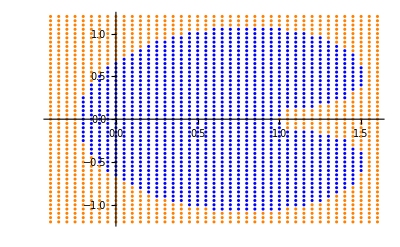

```mathematica
f4=ListPlot[{b,o},PlotStyle->{Blue,Orange},PlotRange->{{-0.4,1.6},{-1.2,1.2}}]
```

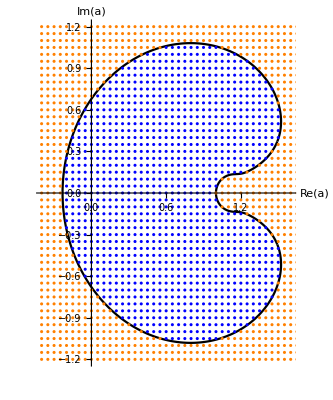

```mathematica
Show[f1,f2,f3,f4]
```

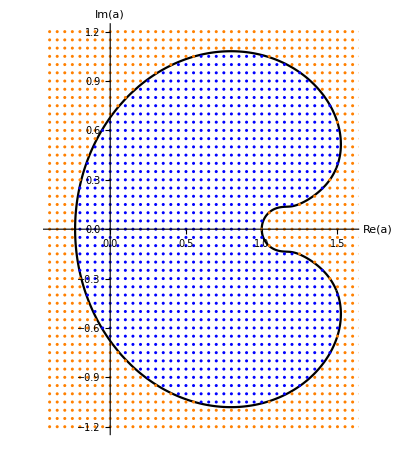
```mathematica
Export["fig8d.pdf",-Graphics-]
```

fig8d.pdf